# Similarity index

El objetivo de esta investigación es encontrar un indice que nos indique la diferencia que existe entre dos reglas. En el juego de la vida tenemo la regla life pero ademas existe un un conjunto de reglas llamadas life like, es decir, unas reglas que tienen un comportamiento similar, pero ¿Que tan similar? ¿Cuales son los criterios que tenemos que considerar para decir que 2 reglas son similares? Si visualizamos las evoluciones en configuraciones iniciales aleatorias, estas reglas parecen indistinguibles, pues son pequeños patrones los que modifican este comportamiento. Es por esto que en esta investigación se busca medir esta similitud existente entre diferentes reglas basandose en el comportamiento.

Esta ivnestigación esta enfocada principalmente en reglas en una sola dimensión.

## Inheritance properties and knew relations

la regla 0 en cualquier automata celular es siempre la misma, no importan los vecinos, no importa el numero de estados, no importa la dimensionalidad, siempre convertira todas las celulas al estado 0, pero este comportamiento no es exclusivo de la regla 0.
Por ejemplo, la regla mas alta en cualquier configuración tambien convierte todas las celulas al estado mas alto sin importar los vecinos. La primer tarea es encontrar aquellas relaciones que son exactas, aquellas reglas que muestran exactamente el mismo comportamiento.

Vamos a iniciar con las configuraciones mas sencillas, un automata celular sin dimensión. El unico vecino de este CA es el mismo, porque lo que podria considerarse como una maquina que evoluciona y que su unico conocimiento es su estado previo. Si consideramos unicamente 2  estados, entonces tenemos el mismo comportamiento que un flip flop, pero podemos llevarlo un poco mas lejos y decir que unicamente tiene un estado, de esta forma tenemos la regla , la cual es la primer regla en existir con la definición mas pequeña y es la unica que pertenece al mismo espacio:

```mathematica
RulePlot[CellularAutomaton[{0,1,0}],ImageSize->100,PlotLegends->Placed[Subscript[0,2,1], Below]]
```

-Graphics-

Ahora podemos realizar 3 cambios al espacio de los automatas celulares, incrementar el numero de estados, el numero de vecinos y la dimensionalidad. Iniciemos entonces incrementando el numero de estados:

Para 2 estados, podemos generar las siguientes  reglas:

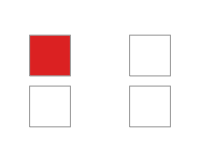
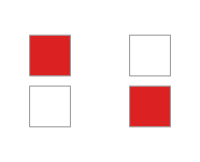
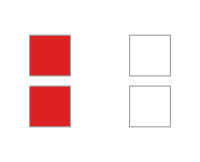
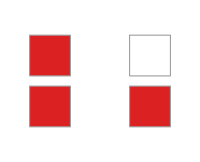
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{RulePlot[CellularAutomaton[{#,2,0}],ColorRules->colorRules[1],ImageSize->200,PlotLegends->Placed[Subscript[#,2,1], Below]]&/@Range[0,3,1]}]
```

Como ya se menciono, dentro de estas reglas existen algunas que tienen el mismo comportamiento, el cual podemos identificar como permutación de estados, es decir, si tenemos 2 automatas celulares cuyos estados son {a,b} y {c,d} y existe una función que mapee {a,b} -> en {c,d} de tal forma que se conservan todas las relaciones en la función de transición podemos decir que esas reglas son identicas.

Para este caso, si realizamos los siguientes mapeos de las reglas:{0, 1} ->{a,b} y {1,0} ->{b,a} encontramos que la regla  y  son equivalente. Esto podemos visualizarlo como si simplemente hicieramos un cambio en los colores:

```mathematica
Grid[{RulePlot[CellularAutomaton[{#,2,0}],ColorRules->colorRules[1],ImageSize->100,PlotLegends->Placed[Subscript[#,2,1], Below]]&/@{0,3},
RulePlot[CellularAutomaton[{#,2,0}],ColorRules->{1->RGBColor[1., 1., 1.],0->RGBColor[0.857359, 0.131106, 0.132128]},ImageSize->100,PlotLegends->Placed[Subscript[#,2,1], Below]]&/@{0,3}}]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

La permutación de estados no es unica de 2 estados, en este caso es sencillo porque es cambiar uno por otro, cuando tenemos mas estados, la permutación de estados nos dice que si mapearamos todos los estados por todas las posibles permutaciones. Este es el caso para 3 estados:

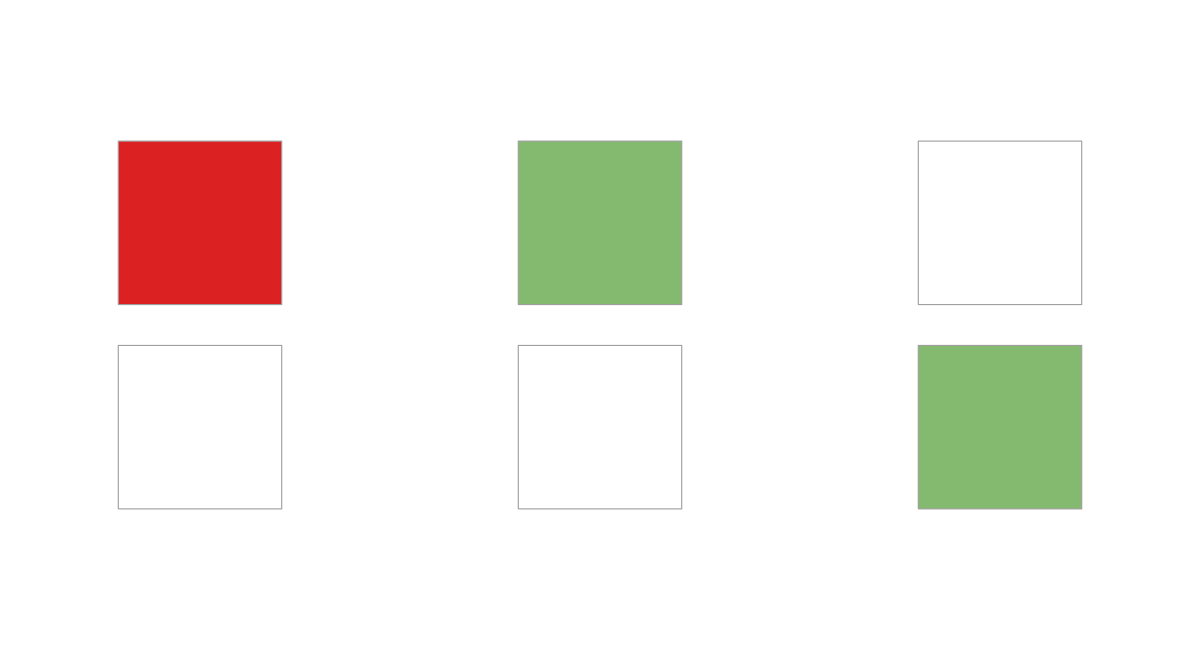
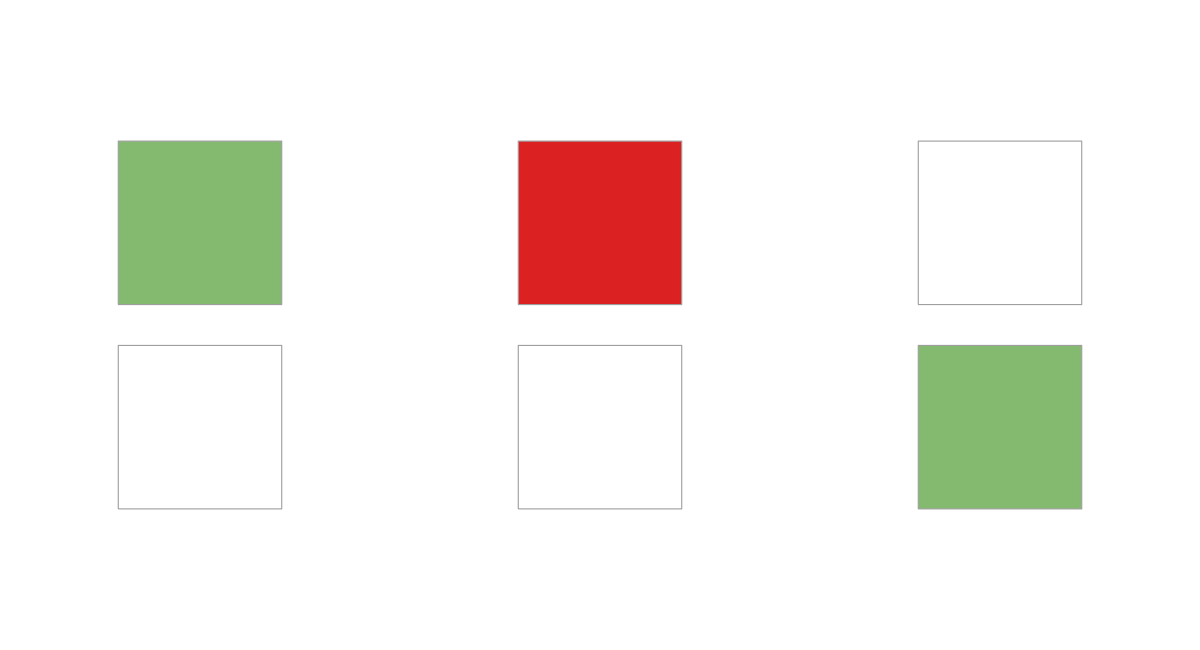
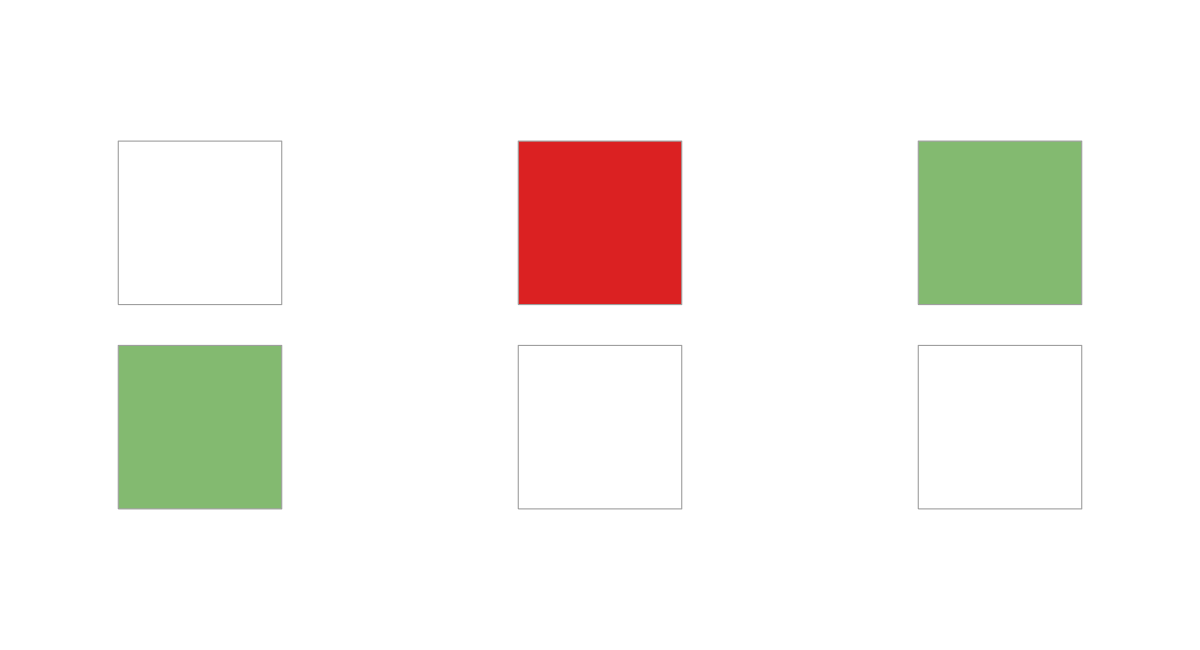
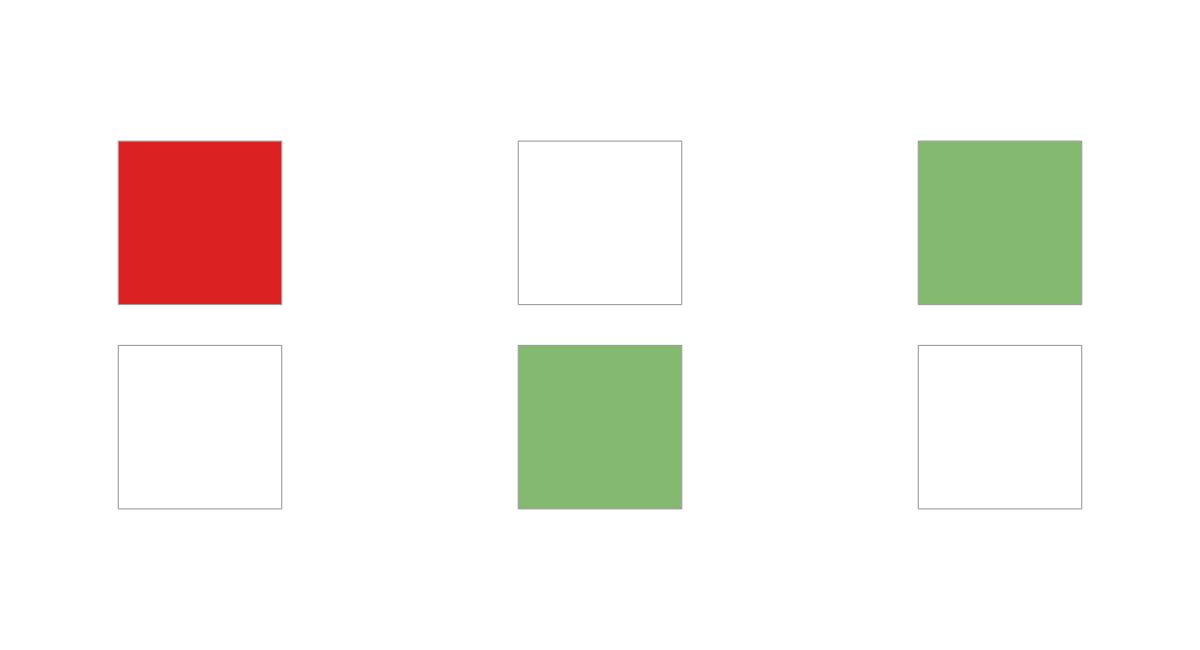
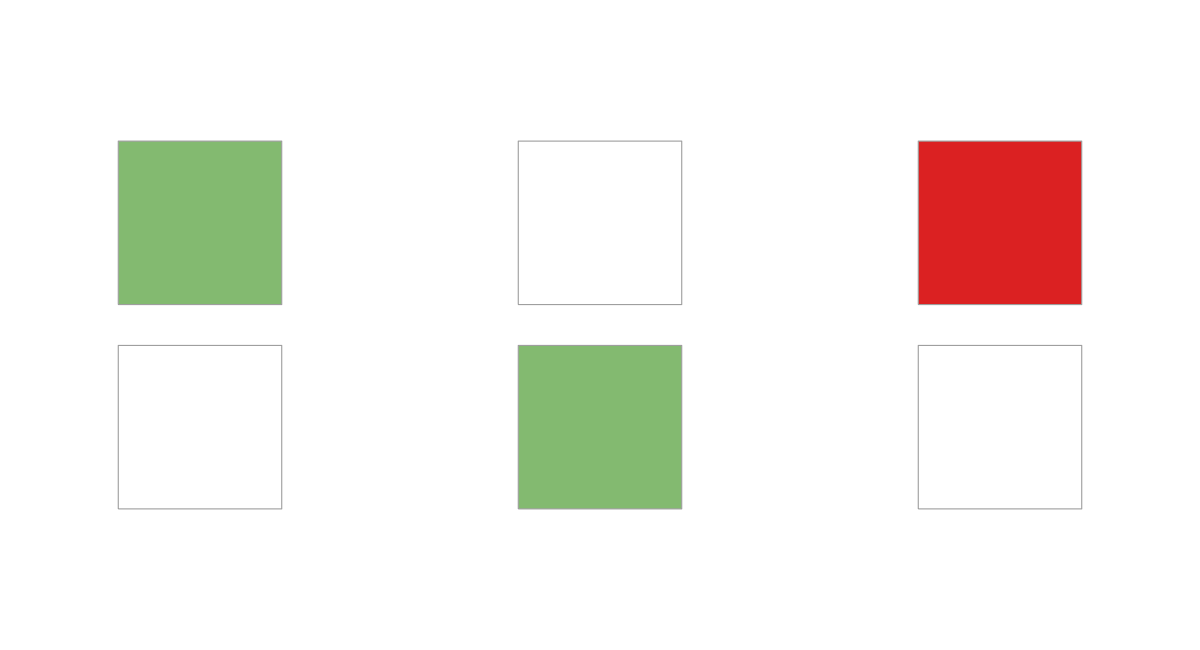
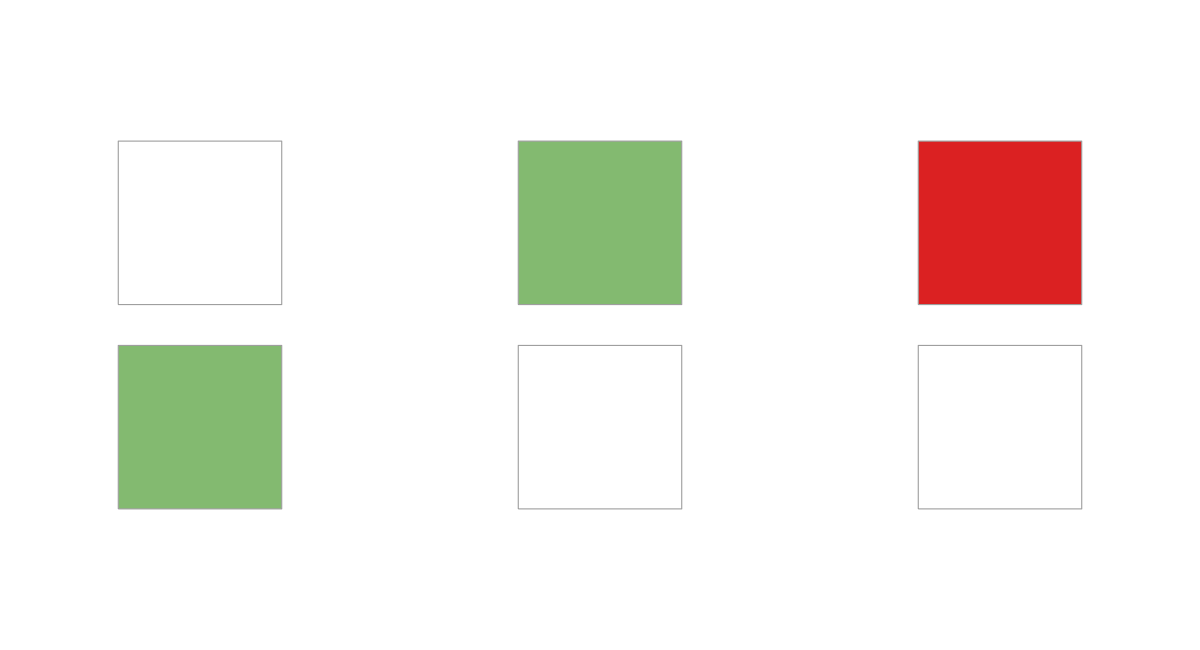
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
crs={{0->RGBColor[1., 1., 1.],1->RGBColor[0.513417, 0.72992, 0.440682],2->RGBColor[0.857359, 0.131106, 0.132128]},{0->RGBColor[1., 1., 1.],2->RGBColor[0.513417, 0.72992, 0.440682],1->RGBColor[0.857359, 0.131106, 0.132128]},{2->RGBColor[1., 1., 1.],0->RGBColor[0.513417, 0.72992, 0.440682],1->RGBColor[0.857359, 0.131106, 0.132128]},{1->RGBColor[1., 1., 1.],0->RGBColor[0.513417, 0.72992, 0.440682],2->RGBColor[0.857359, 0.131106, 0.132128]},{1->RGBColor[1., 1., 1.],2->RGBColor[0.513417, 0.72992, 0.440682],0->RGBColor[0.857359, 0.131106, 0.132128]},{2->RGBColor[1., 1., 1.],1->RGBColor[0.513417, 0.72992, 0.440682],0->RGBColor[0.857359, 0.131106, 0.132128]}};
Grid[Partition[Labeled[CaRulePlot[#[[1]],ColorRules->#[[2]]],#[[1]]]&/@Transpose[{InverseRules[],crs}],3]]
```

Si ocnsideramos que todas estas reglas tienen el mismo comportamiento, entonces el numero de comportamientos es menor al numero de reglas, el cual podemos apreciarlos como se reduce drasticamente el numero total de comportamientos como se incrementa el numero de estados.

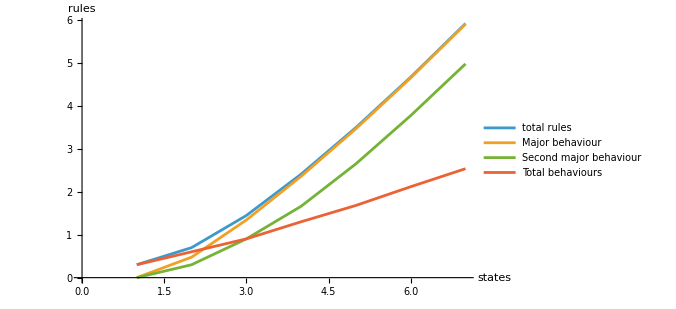

```mathematica
urs=;
ListLinePlot[
Transpose[MapThread[{#1^#1,#2[[-1,1]],If[Length[#2]>=2,#2[[-2,1]],0],Length[#2]}&,{Range[7],urs}]],
ScalingFunctions->"SignedLog",
PlotLegends->{"total rules","Major behaviour","Second major behaviour","Total behaviours"},
ImageSize->500,
AxesLabel->{"states", "rules"}
]
```

En el siguiente plot se muestran los vectores de regla de los comportamientos unicos. Podemos observar, que las reglas con  estados, son un subconjunto de las reglas con  estados donde el nuevo estado tiene una transición a 0

```mathematica
burs=Table[IntegerDigits[#,Max[2,i],i]&/@urs[[i,;;,1]],{i,1,Length[urs]}];
Module[{cell=10,maxRows=50},
Grid[{With[{nrows=Min[maxRows,Dimensions[#][[1]]],
ncols=Dimensions[#][[2]]},
ArrayPlot[#[[;;UpTo[maxRows]]],
ColorRules->colorRules[5],
Mesh->True,
MeshStyle->Directive[GrayLevel[0.4],AbsoluteThickness[0.75]],
PlotRangePadding->0,
ImagePadding->{{0,0},{cell*(maxRows-nrows),0}},
ImageSize->{cell*ncols,cell*maxRows}]]&/@burs
},Spacings->{2, 0}]
]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

La siguiente hipotesis era que existe un mapeo entre las reglas que nos permite movernos entre espacios de CAs. Es decir, nosotros podemos movernos de la regla  a la  unicamente añadiendo un nuevo estado que apunte al estado 0. Consideremos los siguientes ejemplos, donde se muestra con el patrón es exactamente el mismo sin importar cuantos estados añadamos

Reglas {0,0,0,0,0,0,0}:

```mathematica
urv=Join[{<|"ca"->{0,1,0},"vector"->{0,0,0,0,0,0,0}|>},Table[
<|
"ca"->{#,i+1,0},
"vector"->IntegerDigits[#,Max[2,i+1],Length[urs]]
|>&/@urs[[i+1,;;,1]],
{i,1,Length[urs]-1}
]]//Flatten;
Module[{cas=CellularAutomaton[#,Range[#[[2]]-1,0,-1],3]&/@Select[urv,#["vector"]=={0,0,0,0,0,0,0}&][[2;;,"ca"]],cell=15},With[{maxRows=Max[Dimensions[#][[1]]&/@cas]},Grid[{With[{nrows=Dimensions[#][[1]],ncols=Dimensions[#][[2]]},ArrayPlot[#,ColorRules->colorRules[6],Mesh->True,PlotRangePadding->0,ImagePadding->{{0,0},{cell*(maxRows-nrows),0}},ImageSize->{cell*ncols,cell*maxRows}]]&/@cas}]]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Reglas {0,0,0,0,0,0,1}:

```mathematica
urv=Join[{<|"ca"->{0,1,0},"vector"->{0,0,0,0,0,0,0}|>},Table[
<|
"ca"->{#,i+1,0},
"vector"->IntegerDigits[#,Max[2,i+1],Length[urs]]
|>&/@urs[[i+1,;;,1]],
{i,1,Length[urs]-1}
]]//Flatten;
Module[{cas=CellularAutomaton[#,Range[#[[2]]-1,0,-1],3]&/@Select[urv,#["vector"]=={0,0,0,0,0,0,1}&][[2;;,"ca"]],cell=15},With[{maxRows=Max[Dimensions[#][[1]]&/@cas]},Grid[{With[{nrows=Dimensions[#][[1]],ncols=Dimensions[#][[2]]},ArrayPlot[#,ColorRules->colorRules[6],Mesh->True,PlotRangePadding->0,ImagePadding->{{0,0},{cell*(maxRows-nrows),0}},ImageSize->{cell*ncols,cell*maxRows}]]&/@cas}]]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Reglas {0,0,0,0,1,1,2}:

```mathematica
urv=Join[{<|"ca"->{0,1,0},"vector"->{0,0,0,0,0,0,0}|>},Table[
<|
"ca"->{#,i+1,0},
"vector"->IntegerDigits[#,Max[2,i+1],Length[urs]]
|>&/@urs[[i+1,;;,1]],
{i,1,Length[urs]-1}
]]//Flatten;
Module[{cas=CellularAutomaton[#,Range[#[[2]]-1,0,-1],3]&/@Select[urv,#["vector"]=={0,0,0,0,1,1,2}&][[;;,"ca"]],cell=15},With[{maxRows=Max[Dimensions[#][[1]]&/@cas]},Grid[{With[{nrows=Dimensions[#][[1]],ncols=Dimensions[#][[2]]},ArrayPlot[#,ColorRules->colorRules[6],Mesh->True,PlotRangePadding->0,ImagePadding->{{0,0},{cell*(maxRows-nrows),0}},ImageSize->{cell*ncols,cell*maxRows}]]&/@cas}]]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-

Reglas {0,0,0,0,1,1,1}:

```mathematica
urv=Join[{<|"ca"->{0,1,0},"vector"->{0,0,0,0,0,0,0}|>},Table[
<|
"ca"->{#,i+1,0},
"vector"->IntegerDigits[#,Max[2,i+1],Length[urs]]
|>&/@urs[[i+1,;;,1]],
{i,1,Length[urs]-1}
]]//Flatten;
Module[{cas=CellularAutomaton[#,Range[#[[2]]-1,0,-1],3]&/@Select[urv,#["vector"]=={0,0,0,0,1,1,1}&][[;;,"ca"]],cell=15},With[{maxRows=Max[Dimensions[#][[1]]&/@cas]},Grid[{With[{nrows=Dimensions[#][[1]],ncols=Dimensions[#][[2]]},ArrayPlot[#,ColorRules->colorRules[6],Mesh->True,PlotRangePadding->0,ImagePadding->{{0,0},{cell*(maxRows-nrows),0}},ImageSize->{cell*ncols,cell*maxRows}]]&/@cas}]]]
```

-Graphics- | -Graphics- | -Graphics-

Podemos realizar el proceso inverso y eliminar estados. para esto se tienen que satisfacer 2 condiciones:

El ultimo estado debe transicionar a 0

Ningun estado debe de transicionar al ultimo estado

Sin embargo, al quierer aplicar esta reducción encontramos que falla en algunas reglas, por ejemplo :

```mathematica
Grid[{Module[{cas={CellularAutomaton[{31,5,0},Range[4,0,-1],5],CellularAutomaton[{21,4,0},Range[3,0,-1],5],CellularAutomaton[{13,3,0},Range[2,0,-1],5]},labels={Subscript[31,5,1],Subscript[21,4,1],Subscript[13,3,1]},cell=30},With[{maxRows=Max[Dimensions[#][[1]]&/@cas]},MapThread[With[{nrows=Dimensions[#1][[1]],ncols=Dimensions[#1][[2]]},ArrayPlot[#1,ColorRules->colorRules[4],Mesh->True,PlotRangePadding->0,PlotLabel->#2,ImagePadding->{{0,0},{cell*(maxRows-nrows),0}},ImageSize->{cell*ncols,cell*maxRows}]]&,{cas,labels}]]]}]
```

-Graphics-

ya que la reglas   ni  no pertenencen a la lista de comportamientos unicos. Pero podemos encontrar la similitud con la permutación de estados y navegar en el grafo de conexiones, tal como se muestra a conitnuacipón:

```mathematica
Module[{
vectors={{0,0,1,1,1},{0,1,1,1},{1,1,1},{0,0,0},{0,0},{0},{0,0,2,0},{0,2,0},{0,1,1},{1,1}},
edges={{0,0,1,1,1}->{0,1,1,1},{0,1,1,1}->{1,1,1},{1,1,1}->{0,0,0},{0,0,0}->{0,0},{0,0}->{0},{0,1,1,1}->{0,0,2,0},{0,0,2,0}->{0,2,0},{0,2,0}->{0,1,1},{0,1,1}->{1,1},{1,1}->{0,0}},
colores={({0,0,1,1,1}->{0,1,1,1})->Red,({1,1}->{0,0})->Blue,({0,1,1,1}->{1,1,1})->Red,({0,0,0}->{0,0})->Red,({0,0}->{0})->Red,({0,0,2,0}->{0,2,0})->Red,({0,1,1}->{1,1})->Red,({1,1,1}->{0,0,0})->Blue,({0,1,1,1}->{0,0,2,0})->Blue,({0,2,0}->{0,1,1})->Blue}},
Legended[LayeredGraph[
Graph[
edges,
EdgeStyle->colores,
VertexShapeFunction->(Inset[
ArrayPlot[{#2},
ColorRules->colorRules[2],
ImageSize->{Length[#2]*20,20},
Mesh->True,
MeshStyle->Gray,
ImagePadding->0,
PlotRangePadding->0
],#1]&),
VertexSize->{0.01,0.25}],
ImageSize->{450,Automatic}
],LineLegend[colores[[All,2]],{"Delete last state","Minor inverse rule"}]]
]
```

-Graphics-

Con estos 2 tipos de relaciones podemos definir las siguientes conexiones, donde cada nivel representa el numero de estados, cada etiqueta representa la regla representante de cada comportamiento unico y cada flecha es la reducción de estados, no es sorpresa que la mayoria de las conexiones son hacia la regla , recordando que esto es unicamente para CA sin dimensión.

El siguiente paso es incrementar la dimensionalidad y por ende el numero de vecinos, inciando con dos vecinos y 2 estados. Podemos aplicar nuevamente la reducción por permutación de estados, dandonos las siguientes reglas

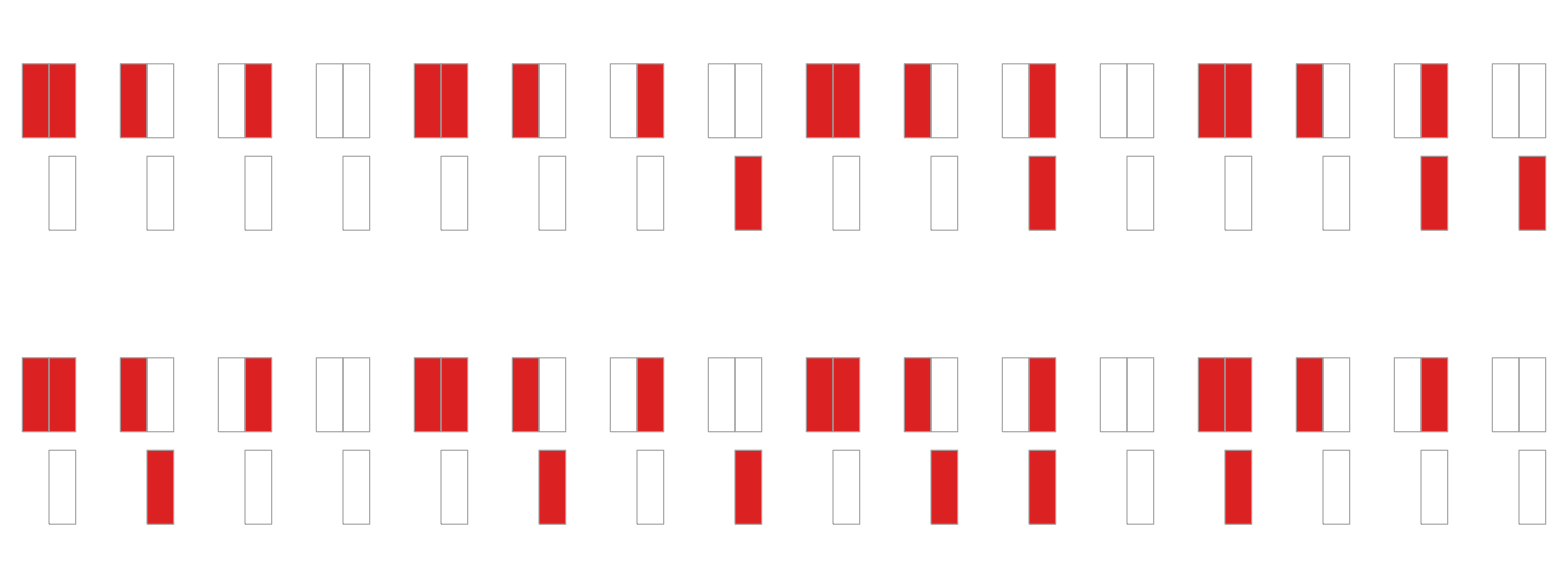

```mathematica
assoc=#[[1]]->#&/@DeleteDuplicates[InverseRules[Subscript@@{#,2,2}]&/@Range[0,15]];
Grid[Partition[CaRulePlot[Subscript@@#[[1]]]&/@assoc,4]]
```

Ahora, encontramos otra similitud de comportamiento, y son aquellas reglas que si invertimos la evolución, obtenemos el mismo comportamiento, tal es el caso de las siguiente 2 reglas:

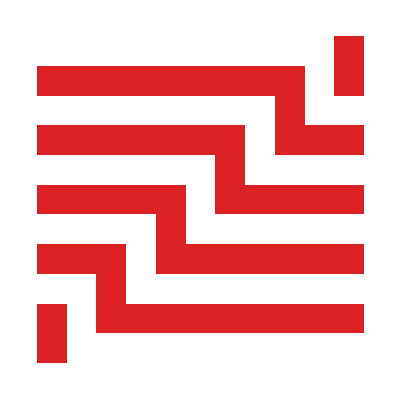
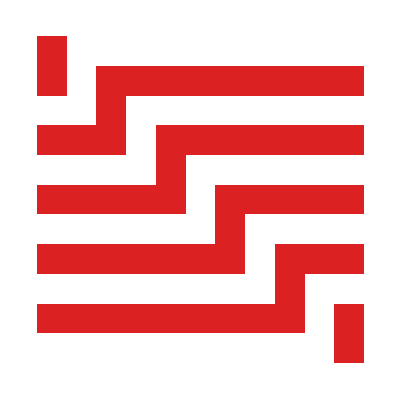
-Graphics- | -Graphics-

```mathematica
init={{1},0};
Grid[{{
RulePlot[CellularAutomaton[{3,2,ReverseSort[{{0},{1}}]}],init,10,PlotLegends->"Text",ColorRules->colorRules[1]],
RulePlot[CellularAutomaton[{5,2,ReverseSort[{{0},{-1}}]}],init,10,PlotLegends->"Text",ColorRules->colorRules[1]]}
}]
```

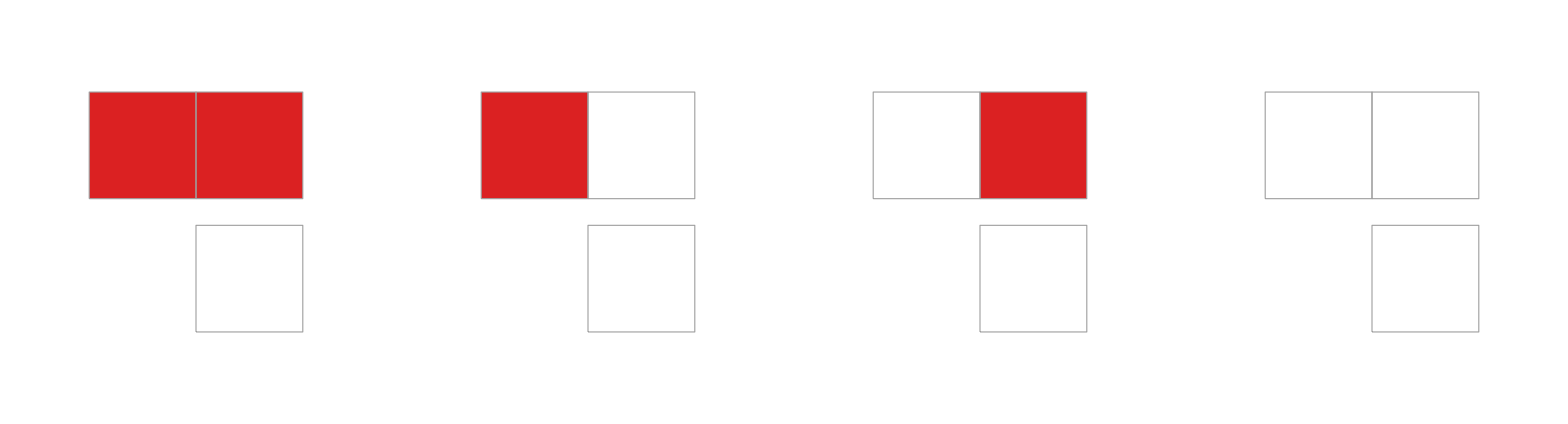
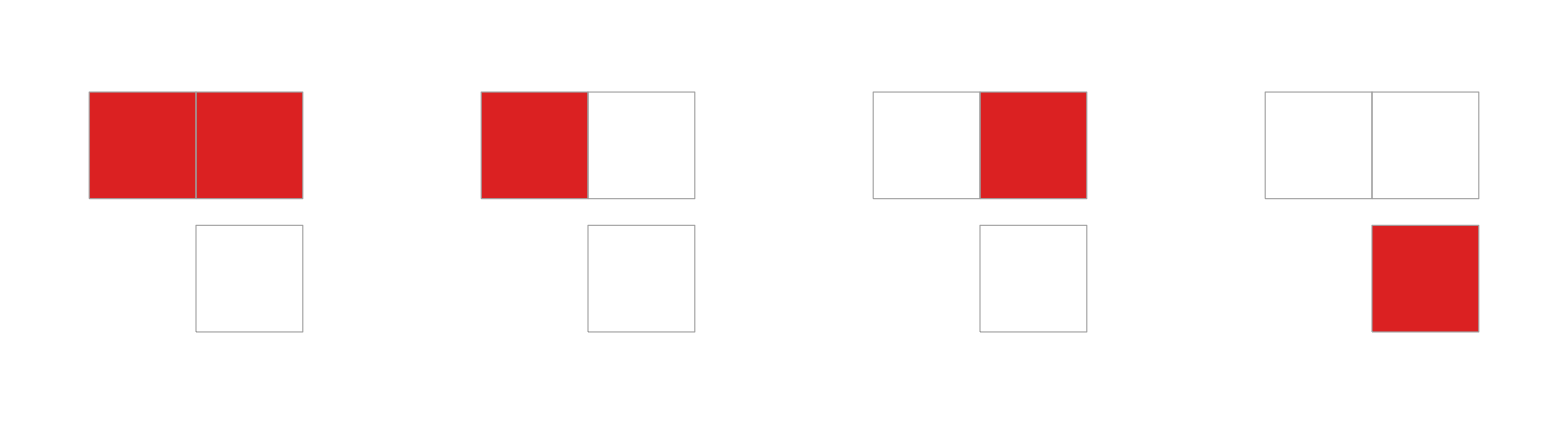
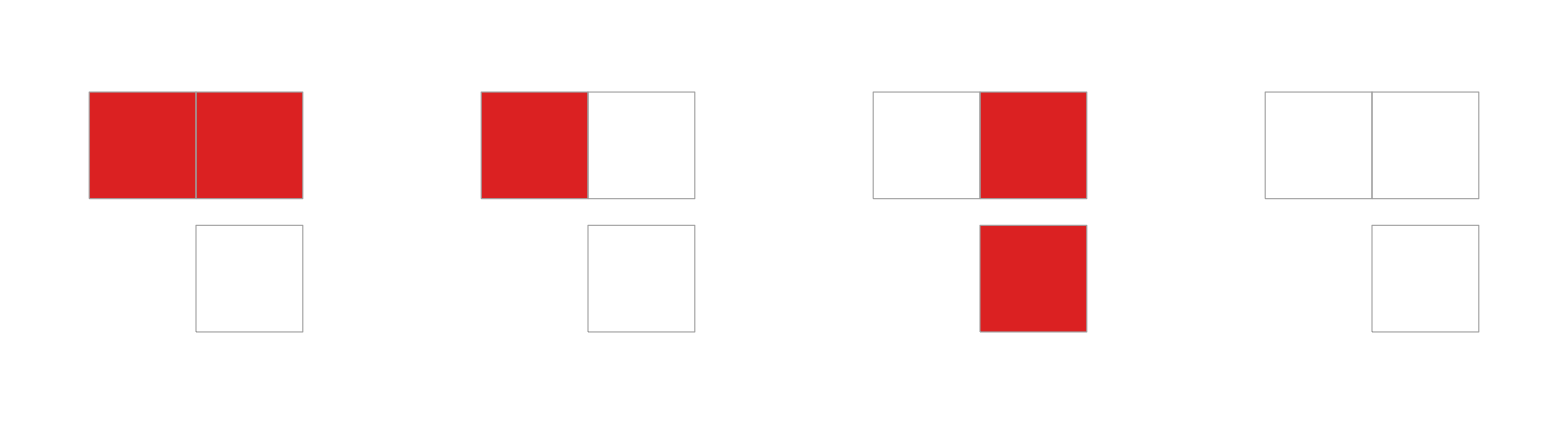
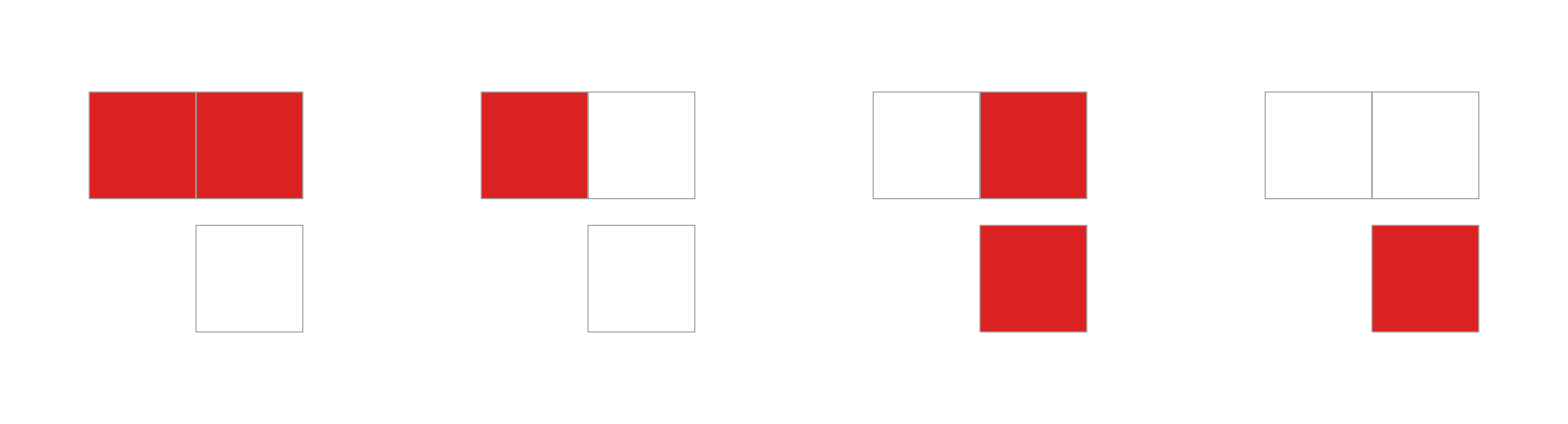
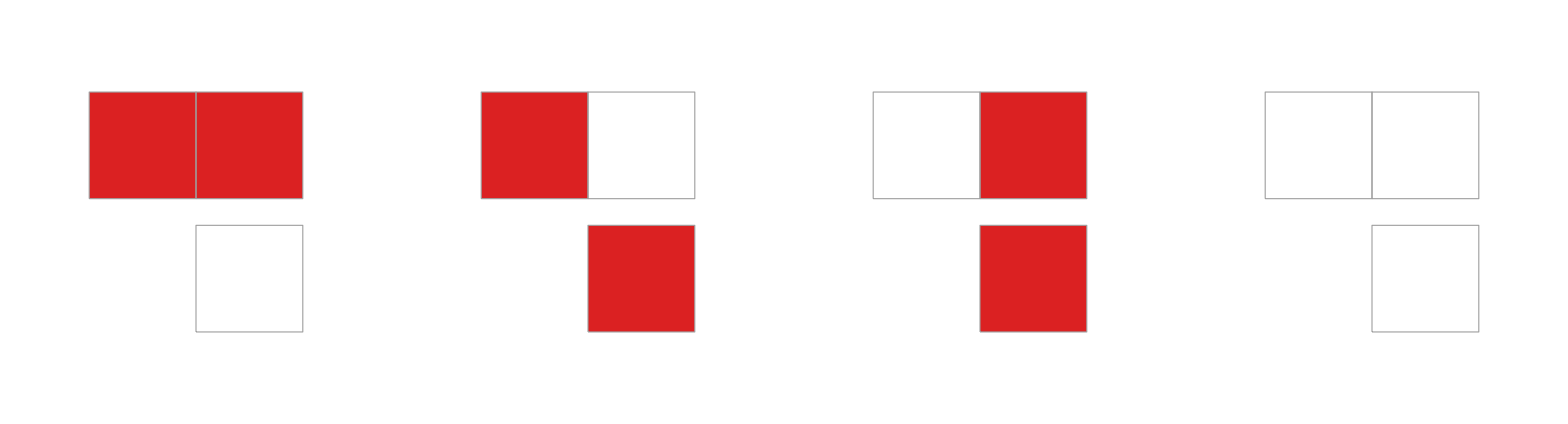
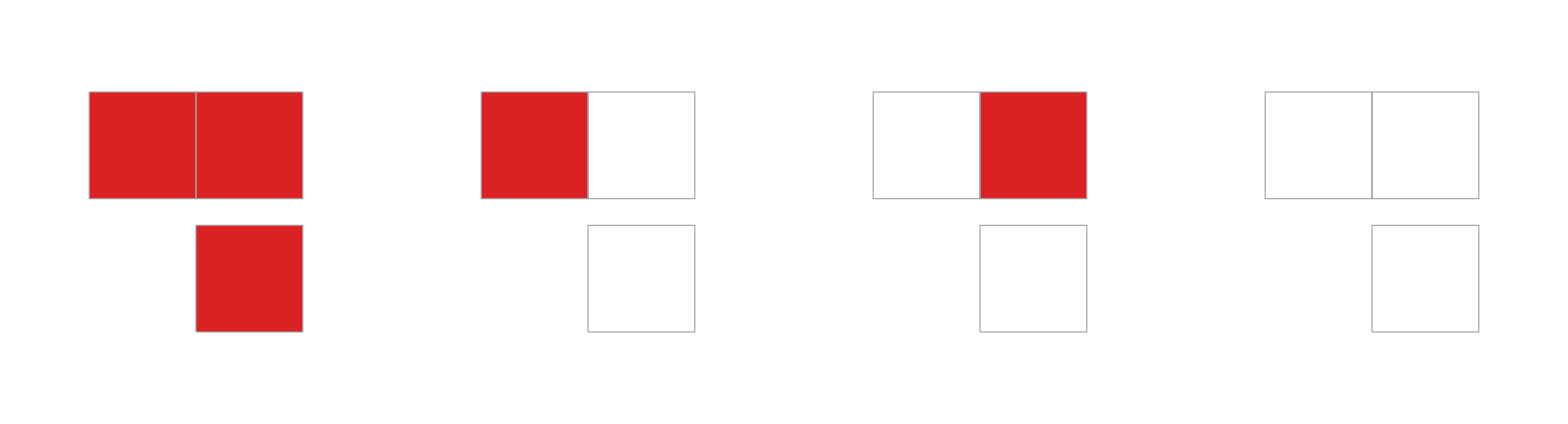
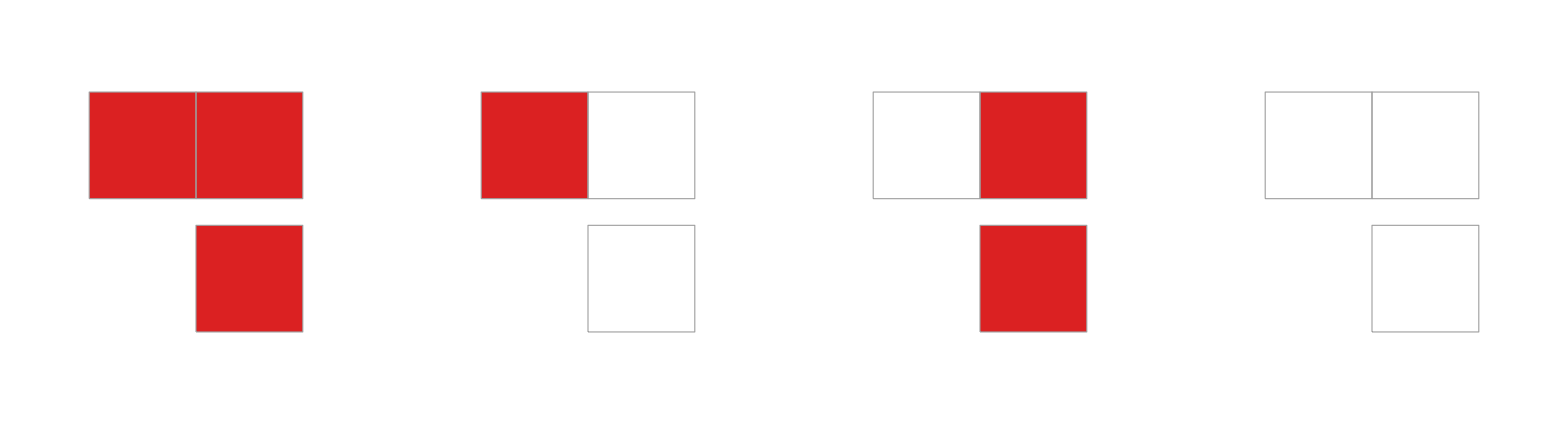
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Grid[Partition[CaRulePlot[Subscript@@{#,2,2}]&/@{0,1,2,3,6,8,10},UpTo[4]]]
```

De estos comportamientos, encontramos 3 relaciones con configuraciones previas.

La regla  no depende de ninguno, al igual que  y

La regla  unicamente depende del vecino de la izquierda, por lo que imita a la regla

La regla  unicamente depende del vecino de la derechoa, por l oque imita a la regla

```mathematica
Grid[{{rulialGraph[{{0,2,1/2}->{0,1,1/2},{0,1,1/2}->{0,1,0},{0,2,1/2}->{0,2,0},{0,2,0}->{0,1,0}},Red],
rulialGraph[{{3,2,1/2}->{1,2,0}},Red],
rulialGraph[{{10,2,1/2}->{2,2,0}},Red]}}]
```

-Graphics-

Las evoluciones de las reglas  y  son exactamente iguales. Para la regla  y  hay que considerar que es el inverso de la celula a la izquierda, por lo que si trasladamos los bloques, a la izquierda, encontramos el mismo comportamiento.

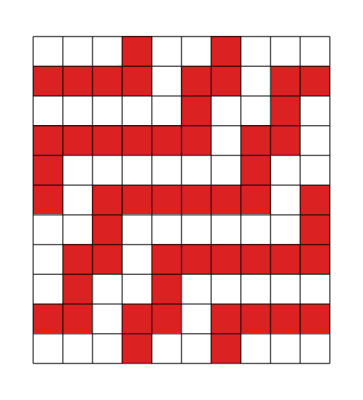
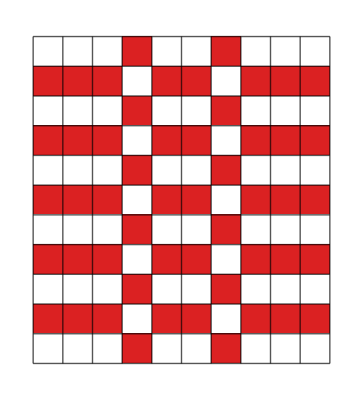
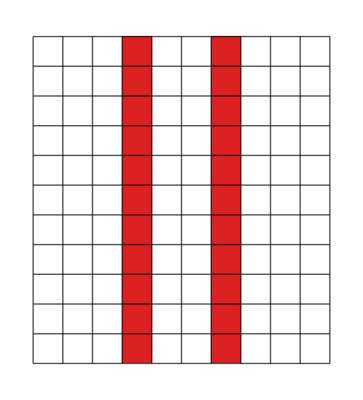
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
init={0,0,0,1,0,0,1,0,0,0};
Grid[{RulePlot[CellularAutomaton[#],init,10,PlotLegends->"Icon",ColorRules->colorRules[1],Mesh->True]&/@{{3,2,1/2},{1,2,0},{10,2,1/2},{2,2,0}}
}]
```

Al final, tenemos solo 4 comportamientos unicos:

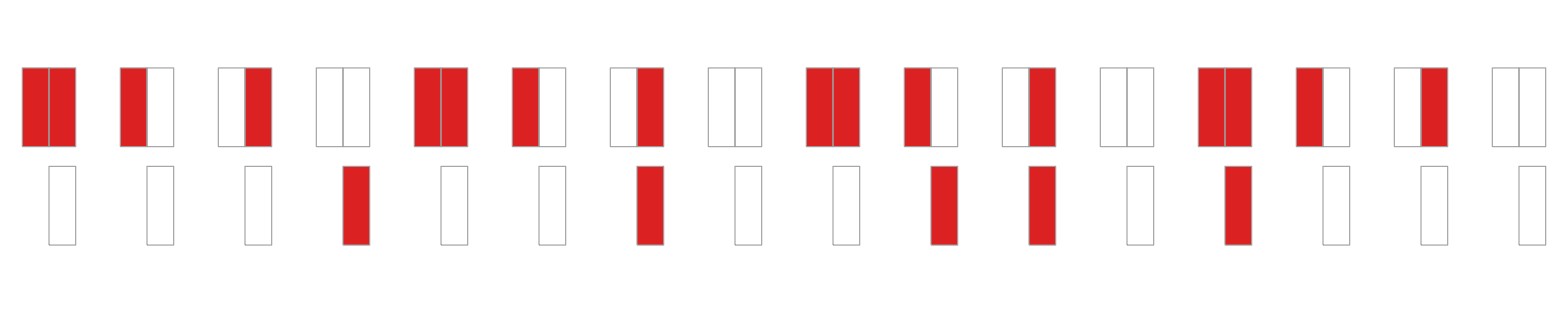

```mathematica
Grid[{CaRulePlot[Subscript@@{#,2,2}]&/@{1,2,6,8}}]
```

Con semillas aleatorias, encontramos los siguientes comportamientos, ninguna de ellas es reversible.

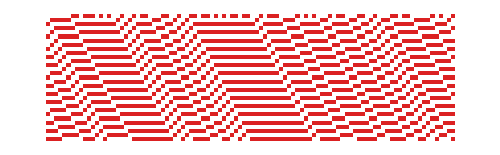
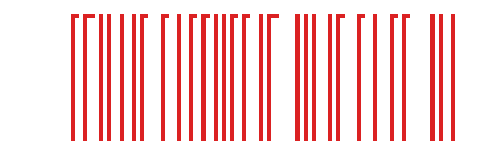
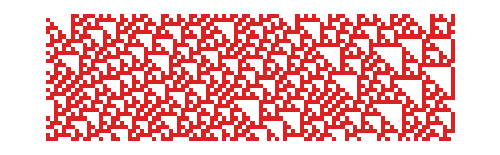
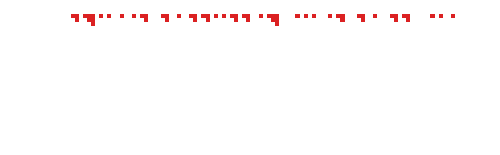
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
init=RandomInteger[{0,1},100];
Grid[Partition[RulePlot[CellularAutomaton[{#,2,1/2}],init,30,ColorRules->colorRules[1],ImageSize->500,PlotLegends->"Icon"]&/@{1,2,6,8},2]]
```

Las funciones de similitud nos dicen que 2 reglas tienen el el mismo comportamiento dentro del mismo espacio. Las reglas de herencia significan que son reglas cuyo comportmaiento puede ser obtenido mediante una regla ya sea con menos estados o con menos vecinos. El ultimo paso de esta investigación es la reducción de dimensionalidad. Es el paso mas complejo porque hasta ahora los vecinos siempre estan agrupados. Si decimos que tenemos 2 vecinos suponemos que esos 2 vecinos son los 2 vecinos mas cercanos, porque verlo en una linea es bastante sencillo, el problema es intentar verlo ahora en 2 dimensiones. Por proximidad, yo puedo decir que los 2 vecinos mas cercanos tienen 2 posibilidades:

```mathematica
Grid[{{ArrayPlot[{{0,0,0},{1,2,1},{0,0,0}},ColorRules->colorRules[2],Mesh->True],ArrayPlot[{{0,1,0},{1,2,0},{0,0,0}},ColorRules->colorRules[2],Mesh->True]}}]
```

-Graphics-

Y ambos tienen comportamientos totalmente diferentes, porque aunque el numero de reglas y del vector de regla son equivalentes: , uno de ellos tiene una reducción de dimensionalidad porque solo considera los elementos en un eje, en este caso, el primero solo considera la izquierda y la derecha, es indiferente del resto de dimensiones. 
Otro evento que puede pasar, es que ocurra una reducción de vecindad que despues de paso a una reducción de dimensión. 
Adicionalmente, sera necesario empezar a especificar cuuales son las posición de los elementos, porque por ejemplo, hasta el momento, hemos considerado que los vecinos siempre son los mas cercanos al centro, incluso si solo son 2, pero no hemos verificado si esto se cumple para cualquiera 2 vecinos que tomemos. Porque existen algunas configuraciones en donde si es verdad pero otras en donde es necesario indagar a profundidad.

Por ejemplo, ¿las siguientes 5 reglas son las mismas? Nosotros estamos asumiendo que si, pero la unica diferencia es que vecinos estamos tomando. Entonces bajo la definición que estuvimos manejando, todas son la regla , pero sus vecinos estan en diferentes posiciones, que si miramos vbien parecen que tienen el mismo comportamiento pero que unicamente tienen un desplazamiento o un remapeo, pero el comportamiento parece ser el mismo para todos. El triangulo de Sierpinsky pertenece a otro espacio de regla.

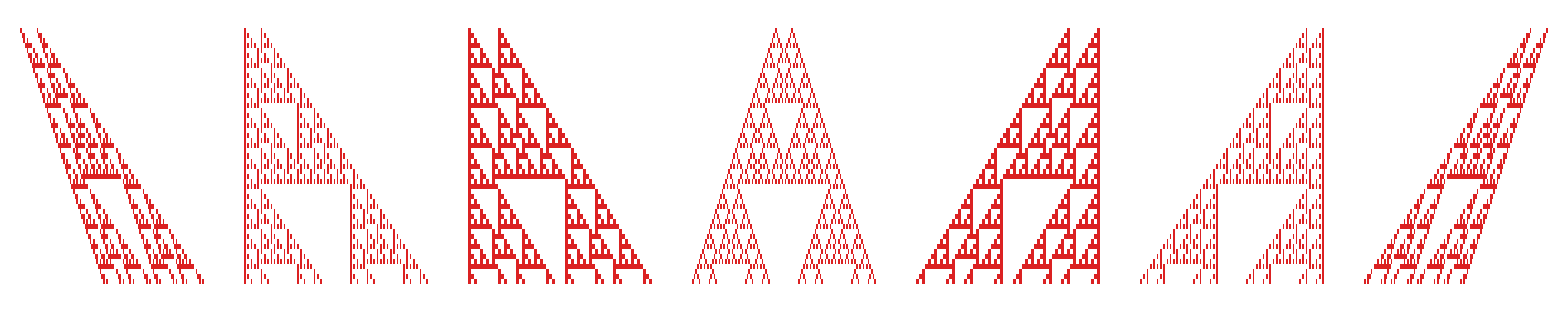

```mathematica
init={{0,0,1,0,0,0,0,0,0,0,0,0,1,0,0},0};
Grid[{{
ArrayPlot[CellularAutomaton[{6,2,{{-2},{-1}}},init,50],ColorRules->colorRules[1]],
ArrayPlot[CellularAutomaton[{6,2,{{-2},{0}}},init,50],ColorRules->colorRules[1]],
ArrayPlot[CellularAutomaton[{6,2,{{-1},{0}}},init,50],ColorRules->colorRules[1]],
ArrayPlot[CellularAutomaton[{6,2,{{-1},{1}}},init,50],ColorRules->colorRules[1]],
ArrayPlot[CellularAutomaton[{6,2,{{0},{1}}},init,50],ColorRules->colorRules[1]],
ArrayPlot[CellularAutomaton[{6,2,{{2},{0}}},init,50],ColorRules->colorRules[1]],
ArrayPlot[CellularAutomaton[{6,2,{{2},{1}}},init,50],ColorRules->colorRules[1]]
}}]
```

Con los siguientes datos precargados, mostramos todas las relaciones descubertas para los CAs con configuraciones relativamente pequeñas:

```mathematica
data=addData[Join[getRules[2,1],getRules[3,1],getRules[2,2],getRules[3,2]]];
```

```mathematica
rdata=reduce[data];
```

Sin embargo, todos los experimentosrealizados hasta el momento unicamente nos indican si 2  reglas tienen el mismo comprotamiento o no, una clasificación binaria que no nos dice que tan parecidas son dichas reglas basadas en sus comportamientos, bajo este metodo, descrubririamos que las reglas life like son totalmente diferentes de la regla life, lo que es contraintuitivo. El siguiente paso para encontrar la similitus entre las reglas es comparar las evoluciones en el grafo de evoluciones.

## Evolution graph

Para esta parte, lo que haremos sera evolucionar un automata celular en todos los posibles espacios finitos. Con esto buscaremos construir un grafo de transiciones que nos permita comparar el comparar elcomprotamiento de sus transiciones, buscando una similitud entre dichos elementos.  Tomemos como ejemplo la regla 0 y la regla 255 de ECA en un espacio de 5 celulas:

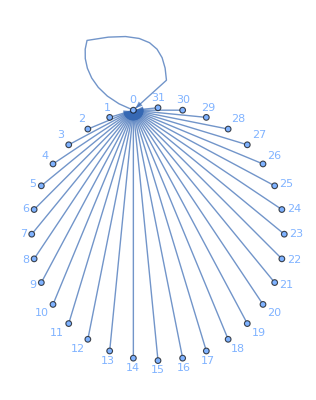
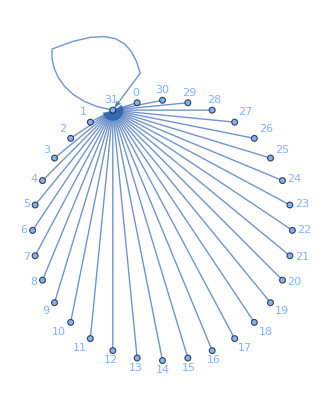
-Graphics-0_(2,3) | -Graphics-255_(2,3)

```mathematica
inits=Tuples[Range[0,1],5];
r255=FromDigits[#[[1]],2]->FromDigits[#[[2]],2]&/@(CaArray[Subscript[255,2,3],#,1]&/@inits);
r0=FromDigits[#[[1]],2]->FromDigits[#[[2]],2]&/@(CaArray[Subscript[0,2,3],#,1]&/@inits);
Grid[{{Labeled[Graph[r0,VertexLabels->Automatic,GraphLayout->"CircularEmbedding"],],Labeled[Graph[r255,VertexLabels->Automatic,GraphLayout->"CircularEmbedding"],]}},Frame->All]
```

Cada nodo es un espacio representado en su forma decimal, cada nodo tiene unicamente una transicion a otra configuración. Vemos qu las reglas  y  tienen exactamente la misma forma pero difieren en las etiquetas. 
Podemos decir que estos 2 grafos son isomorficos, es decir, existe una función biyectiva que puede mapear cada vertice en la matriz de transición, en este caso, cambiando el 0 por el 31

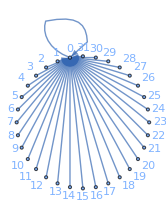
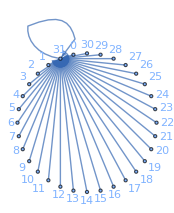
```mathematica
IsomorphicGraphQ[-Graphics-,-Graphics-]
```

True

Si verificamos solo si son isomorficos tenemos nuevamente las mismas relaciones que ya conocemos y con la misma clasificación entre 0 y 1. Para esto se propusieron 3 experimentos con reusltados similiares:

## Cannonical Form

podemos tambien usar la forma canonica, que es una expresion que muestra la topologia de un grafo sin interesarnos en su estructura. Este metodo unicamente nos permiter realizar comparaciones booleanas, pero nos sirve para identificar y contar el numero de estructuras existentes. Para codificar esto, usamos el siguiente algoritmo de renombramiento:

Eliminmaos todos los nodos hojas y y los añadimos a una cola

Para cada nodo hoja creaos un codigo que lo relacione con su nodo padre y eliminamos el nodo

Si el nodo padre se convierte en un nodo hoja lo eliminamos y se añade a la cola

Al finalizar con todos los nodos hojas, se codifican los ciclos resultantes

Es decir, se hace una poda hasta llegar a los ciclos, preservando todas las relaciones que se hayan encontrado.

```mathematica
CanonFuncGraphQ[-Graphics-,-Graphics-]
```

True

Obtenemos la forma canonica de las reglas de ECA en diferentes tamaños, para encontrar las relaciones.

```mathematica
groups=ParallelTable[Module[{cfs},
cfs={#,CanonFuncGraph[MakeGraph[Subscript[#,2,3],i]]}&/@Range[0,255];
Values[GroupBy[cfs,#[[2]]&]][[;;,;;,1]]
]
,{i,1,12,1}];
```

```mathematica
ListLinePlot[Labeled[#,#]&/@Length/@groups,AxesLabel->{"space size", "behaviours"},InterpolationOrder->0.1,Filling->Bottom]
```

-Graphics-

Entre mas grande sea el espacio mas distinciones podemos hacer entre reglas, pero esta limitación no crece conforme el espacio, sino que tiene una limitación. Para ECA,con 4 espacios podemos difererenciar casi en su totalidad todos los comprotamientos reales o ya clasificados. Esto nos genera otra duda ¿Como podemos definir el tamaño minimo adecuado para no perder información?

Este metodo aunque nos permite encontrar de igual manera las clasificaciones, no nos sirve como indice porque la similitud que se obtiene es exacta, para intentar corregir esto valos a utilizar el siguiente metodo, que calcula los Eigen Values y los utiliza como vector de caracteristicas.

## Eigen Values

Un grafo puede representarse como una matriz, y de dicha matriz podemos obtener los valores propios, un vector de valores que nos dice su nivel de improtancia dentro de la matriz. Para esto, aplicamos el siguiente proceso:

Extraemos la matriz de transición

Calculamos los valores propios de la matriz

Comparamos los 2 vectores con distancia coseno.

```mathematica
ev0=Eigenvalues[N@Normal[AdjacencyMatrix[-Graphics-]]]
ev255=Eigenvalues[N@Normal[AdjacencyMatrix[-Graphics-]]]
```

{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

Si la distancia es 0 significa que las reglas son equivalentes. Pero al no tratarse de una matriz simetrica, es posible que los Eigen Values tengan un dominio imaginario. Para combatir esto podemos duplicar la dimensionalidad en reales y complejos o podemos crear una medida intermediaque los agrupe, como la un coseno.

```mathematica
Eigenvalues[N@Normal[AdjacencyMatrix[MakeGraph[,4]]]]
EigenvaluesGraph[MakeGraph[,4]]
```

{-2.25642×10^-18+1. ⅈ,-2.25642×10^-18-1. ⅈ,-0.707107+0.707107 ⅈ,-0.707107-0.707107 ⅈ,-1.+0. ⅈ,1.+0. ⅈ,-1.+0. ⅈ,0.707107+0.707107 ⅈ,0.707107-0.707107 ⅈ,1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

{-2.25642×10^-18,1.,-2.25642×10^-18,-1.,-0.707107,0.707107,-0.707107,-0.707107,-1.,0.,1.,0.,-1.,0.,0.707107,0.707107,0.707107,-0.707107,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

Podemos aplicar distancia coseno y obtener una medida de similitud entre diferentes reglas. El plot de abajo muestra la relación entre las 256 reglas de ECA.

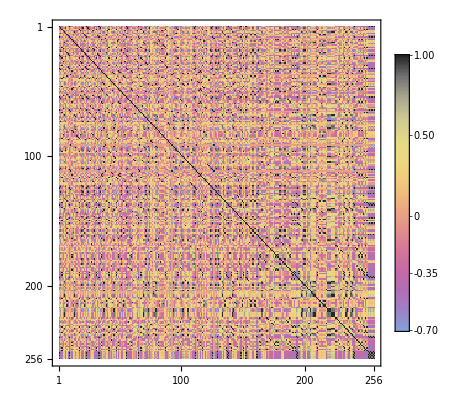

```mathematica
ecaGraphs=ParallelTable[MakeGraph[Subscript[i,2,3],5],{i,0,255,1}];
distances=1-DistanceMatrix[ecaGraphs,DistanceFunction->EigenvaluesGraphDistance];
MatrixPlot[distances,ColorFunction->"CMYKColors",PlotLegends->Automatic]
```

Sin emabrgo, Con este metodo, aunque podemos encontrar las relaciones entre diferentes reglas, surge un problema, y que no podemos comparar reglas de diferentes espacios, ya que el numero de nodos es quien define el tamaño del vector, y no habria forma de mapear las relaciones sin perder información:

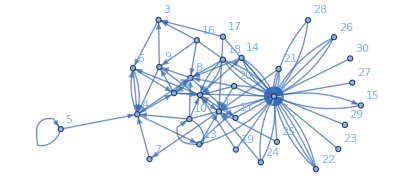
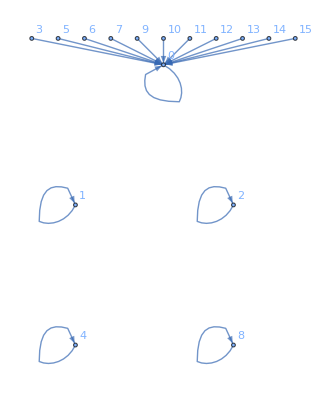
4_(3,2) | 4_(2,4)
-Graphics- | -Graphics-
Total vertex:31 | Total vertex:16
{2.67226,-1.66919,0.436134,0.436134,-1.05038,-1.05038,1.,-1.,1.,1.,-0.174314,-0.174314,-0.275455,-0.275455,0.706521,0.418448,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {1.,1.,1.,1.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Grid[Transpose[Module[{g},
Table[
g=MakeGraph[i,4];
{
i,
g,
"Total vertex:"<>ToString[Length[VertexList[g]]],
Re[Eigenvalues[N[Normal[AdjacencyMatrix[g]]]]]
},
{i,{,}}]
]],
Frame->All
]
```

Es por esto que se utiliza un nuevo metodo, que en lugar de calcular directamente los eigenvalues, realiza un conteo de ciclos en diferentes periodos

## Functions

## Unprotected functions

```mathematica
Unprotect[RulePlot];

Quiet[RulePlot[CellularAutomaton[{0,1,0}],opts:OptionsPattern[]]=.];
Quiet[RulePlot[CellularAutomaton[{0,1,1/2}],opts:OptionsPattern[]]=.];

RulePlot[CellularAutomaton[{0,1,r_}],opts:OptionsPattern[]]:=Module[{imgSize=Lookup[{opts},ImageSize,100],legend=Lookup[{opts},PlotLegends,None],restOpts=FilterRules[DeleteCases[{opts},(ImageSize|PlotLegends|ColorRules)->_],Options[Graphics]],ref,caseGfx,xCoords,xMin,xMax},ref=RulePlot[CellularAutomaton[{0,2,r}]];
caseGfx=ref[[1,1,1,-1]];
xCoords=Sort@Cases[ref[[1,2]],Line[{{x_,_},{x_,_}}]:>x,Infinity];
xMin=xCoords[[-2]];
xMax=Last[xCoords];
With[{g=Graphics[{caseGfx,{GrayLevel[0.8],{Line[{{xMin,0},{xMin,1}}],Line[{{xMax,0},{xMax,1}}]},{Line[{{xMin,0},{xMax,0}}],Line[{{xMin,1},{xMax,1}}]}}},ImageSize->imgSize,Sequence@@restOpts]},If[legend===None,g,Legended[g,legend]]]];

Protect[RulePlot];
```

SetDelayed::write: Tag RulePlot in RulePlot[CellularAutomaton[{0,1,r_}],opts:OptionsPattern[]] is Protected.

## Plot functions

```mathematica
colorRules[n_:10]:=Join[{0->RGBColor[1., 1., 1.]},Table[k->ColorData["Rainbow"][k/(n)],{k,1,(n)}]];
```

```mathematica
CaRulePlot[ca_Subscript,opts:OptionsPattern[]]:=
RulePlot[CellularAutomaton[{ca[[1]],ca[[2]],(ca[[3]]-1)/2}],opts,ColorRules->colorRules[ca[[2]]-1],opts];
```

```mathematica
rulialGraph[trans_,colorA_:Red,colorB_:Blue,labelA_:"Delete Last State",labelB_:"Minor inverse rule"]:=Module[
{
edges=Join[trans[[1]],trans[[2]]],
edgeStyles=Join[(#->Directive[colorA,Thick])&/@trans[[1]],(#->Directive[colorB,Thick])&/@trans[[2]]],
nodePlot=Function[v,If[v[[2]]<1,Graphics[{GrayLevel[0.9],Rectangle[]},ImageSize->{30,25}],RulePlot[CellularAutomaton[v],ImageSize->{Automatic,30},ColorRules->colorRules]]]
},
Legended[
LayeredGraph[
Graph[
edges,
EdgeStyle->edgeStyles,
VertexShapeFunction->(Inset[Column[{nodePlot[#2],Style[Subscript[#2[[1]],#2[[2]],1],Small,Black]},Alignment->Center],#1]&),
VertexSize->{0.11,100.03}
],
ImageSize->{Automatic,Automatic},
AspectRatio->2],
LineLegend[{colorA,colorB},{labelA,labelB}]
]
]
```

## Functions

```mathematica
getRules[s_,n_]:=ParallelMap[Subscript[#,s,n]&,Range[0,s^(s^n)-1]]
```

```mathematica
CaRulePlot[ca_Subscript,opts:OptionsPattern[]]:=
RulePlot[CellularAutomaton[{ca[[1]],ca[[2]],(ca[[3]]-1)/2}],ColorRules->colorRules[ca[[2]]-1],opts];
```

```mathematica
CaArrayPlot[ca_Subscript,s_,t_,opts:OptionsPattern[]]:=
ArrayPlot[CellularAutomaton[{ca[[1]],ca[[2]],(ca[[3]]-1)/2},s,t],ColorRules->colorRules[ca[[2]]-1],opts];
```

```mathematica
CaArray[ca_Subscript,s_,t_]:=Module[{},
CellularAutomaton[{ca[[1]],ca[[2]],(ca[[3]]-1)/2},s,t]
]
```

### Direct relations

```mathematica
addData[rulesIn_List,dataIn_Association:<||>]:=Module[
{
data=dataIn,rules=rulesIn,
inverseRules,mirrorRules,stateRules,neighborRules,joinRules
},
{inverseRules,mirrorRules,stateRules,neighborRules}=Parallelize[{
DeleteDuplicates@Flatten[Table[Map[rule->#&,InverseRules[rule]],{rule,rules}]],
DeleteDuplicates@Flatten[Table[Map[rule->#&,MirrorRules[rule]],{rule,rules}]],
Select[Map[#->DeleteState[#]&,rules],#[[2]]=!=Null&],
Select[Map[#->DeleteNeighbor[#]&,rules],#[[2]]=!=Null&]
}];

<|
"inverse"->DeleteDuplicates[Join[Lookup[dataIn,"inverse",{}],inverseRules]],
"mirror"->DeleteDuplicates[Join[Lookup[dataIn,"mirror",{}],mirrorRules]],
"state"->DeleteDuplicates[Join[Lookup[dataIn,"state",{}],stateRules]],
"neighbor"->DeleteDuplicates[Join[Lookup[dataIn,"neighbor",{}],neighborRules]]
|>
]
```

```mathematica
reduce[data_]:=Module[{dataUnq},
dataUnq=ReplaceAll[data,ParallelMap[Reverse,data["inverse"]]];
dataUnq=ReplaceAll[dataUnq,ParallelMap[Reverse,dataUnq["mirror"]]];
ParallelMap[DeleteDuplicates,dataUnq[[{"inverse","join","state","neighbor"}]]]
]
```

#### InverseRule

```mathematica
InverseRules[ca_Subscript]:=Module[
{
r=ca[[1]],s=ca[[2]],n=(ca[[3]]-1)/2,
L=ca[[2]]^ca[[3]],outputs,tuples,perms,res
},
outputs=Reverse[IntegerDigits[r,s,L]];(*outputs[[k]]=salida de la vecindad k-1*)
tuples=IntegerDigits[#,s,2n+1]&/@Range[0,L-1];(*tuples[[k]]=vecindad k-1 como n-tupla*)
perms=Permutations[Range[0,s-1]];(*solo s! permutaciones de ESTADOS*)
res=Sort@DeleteDuplicates@Table[
Module[
{pi=AssociationThread[Range[0,s-1]->perm],newOut=ConstantArray[0,L]},
Do[
newOut[[FromDigits[pi/@tuples[[k]],s]+1]]=pi[outputs[[k]]]
,{k,1,L}
];
FromDigits[Reverse[newOut],s]]
,{perm,perms}
];
Subscript[#,ca[[2]],ca[[3]]]&/@res
]
```

#### Mirror Rules

```mathematica
MirrorRules[ca_Subscript]:=Module[{pos,rule,assoc,res},
pos=IntegerDigits[#,ca[[2]],ca[[3]]]&/@Range[0,ca[[2]]^ca[[3]]-1];
rule=IntegerDigits[ca[[1]],ca[[2]],Length[pos]];
assoc=Transpose[{pos,rule}];
res=Sort@DeleteDuplicates[{ca[[1]],FromDigits[
SortBy[{Reverse[#[[1]]],#[[2]]}&/@assoc,#[[1]]&][[;;,2]],
ca[[2]]
]}];
Subscript[#,ca[[2]],ca[[3]]]&/@res
]
```

#### Delete state

```mathematica
DeleteState[ca_Subscript]:=Module[{vector,pos,rule,newpos},If[ca[[2]]==1,Return[];];
vector=IntegerDigits[Range[ca[[2]]^ca[[3]]-1,0,-1],ca[[2]]];
pos=Position[vector,ca[[2]]-1][[;;,1]];
rule=IntegerDigits[ca[[1]],ca[[2]],ca[[2]]^ca[[3]]];
If[rule[[pos]]==ConstantArray[0,Length[pos]]&&Not@ContainsAny[rule,{ca[[2]]-1}],
(*Puede eliminarse ese estado*)
newpos=Complement[Range[ca[[2]]^ca[[3]],1,-1],pos];
Subscript[FromDigits[rule[[newpos]],ca[[2]]-1],ca[[2]]-1,ca[[3]]],
(*No puede eliminarse*)
Null]];
```

#### Delete neighbor

```mathematica
DeleteNeighbor[ca_Subscript]:=Module[
{r,s,n,rv,tuples,ruleIdx,indepQ,ip,relPos,nRed,redRV},
r=ca[[1]];s=ca[[2]];n=ca[[3]];
If[n==1,Return[];];
rv=IntegerDigits[r,s,s^n];
tuples=IntegerDigits[#,s,n]&/@Range[s^n-1,0,-1];
ruleIdx[inp_]:=s^n-FromDigits[inp,s];
indepQ[pos_]:=AllTrue[tuples,Function[inp,SameQ@@Table[rv[[ruleIdx[ReplacePart[inp,pos->v]]]],{v,0,s-1}]]];
ip=Select[Range[n],indepQ];
If[Length[ip]==0,Null,relPos=Complement[Range[n],{ip[[1]]}];(*solo elimina 1 posición*)nRed=n-1;
redRV=rv[[ruleIdx[ReplacePart[ConstantArray[0,n],Thread[relPos->#]]]]]&/@(IntegerDigits[#,s,nRed]&/@Range[s^nRed-1,0,-1]);
Subscript[FromDigits[redRV,s],s,n-1]]]
```

### Graph relations

```mathematica
MakeGraph[ca_Subscript,spaceSize_]:=Module[{inits},
inits=Tuples[Range[0,ca[[2]]-1],spaceSize];
Graph[
Map[
FromDigits[#[[1]],2]->FromDigits[#[[2]],2]&,(CaArray[ca,#,1]&/@inits)],
VertexLabels->Automatic]
]
```

```mathematica
EigenvaluesGraph[g_Graph]:=Module[{ev},
ev=Eigenvalues[N[Normal[AdjacencyMatrix[g]]]];
Flatten[Transpose[{Re[ev],Im[ev]}]]
]
```

```mathematica
EigenvaluesGraphDistance[g1_Graph,g2_Graph]:=Module[{ev1,ev2},
ev1=EigenvaluesGraph[g1];
ev2=EigenvaluesGraph[g2];
CosineDistance[ev1,ev2]
]
```

#### Graph relations

```mathematica
CanonFuncGraph[g_Graph]:=Module[{verts,index,f,n,indeg,preds,code,queue,visited,cycles,succ},verts=VertexList[g];n=Length[verts];index=AssociationThread[verts,Range[n]];succ=Association[(#1⟦1⟧->#1⟦2⟧&)/@EdgeList[g]];f=Table[index[succ[v]],{v,verts}];indeg=ConstantArray[0,n];Do[indeg⟦f⟦i⟧⟧++,{i,n}];preds=ConstantArray[{},n];code=ConstantArray[Null,n];queue=Flatten[Position[indeg,0]];While[queue=!={},With[{v=First[queue]},queue=Rest[queue];code⟦v⟧={Sort[preds⟦v⟧]};With[{w=f⟦v⟧},AppendTo[preds⟦w⟧,code⟦v⟧];If[--indeg⟦w⟧==0,AppendTo[queue,w]]]]];visited=ConstantArray[False,n];cycles={};Do[If[indeg⟦v⟧>0&&!visited⟦v⟧,Module[{c={},w=v},While[!visited⟦w⟧,visited⟦w⟧=True;AppendTo[c,w];w=f⟦w⟧];AppendTo[cycles,c]]],{v,n}];Sort[(Module[{seq=({Sort[preds⟦#1⟧]}&)/@#1},First[Sort[Table[RotateLeft[seq,j],{j,Length[seq]}]]]]&)/@cycles]]
```

```mathematica
CanonFuncGraphQ[g1_Graph,g2_Graph]:=Sort[CanonFuncGraph[g1]]===Sort[CanonFuncGraph[g2]]
```

```mathematica
SpectralMoments[g_Graph,kmax_Integer]:=Module[{verts,index,succ,f,n,indeg,resto,queue,qi,v,visited,cycles},verts=VertexList[g];
n=Length[verts];
index=AssociationThread[verts,Range[n]];
succ=Association[(#[[1]]->#[[2]])&/@EdgeList[g]];
f=Table[index[succ[v]],{v,verts}];
indeg=ConstantArray[0,n];
Do[indeg[[f[[i]]]]++,{i,n}];
resto=indeg;
queue=Flatten@Position[resto,0];
qi=1;
While[qi<=Length[queue],v=queue[[qi++]];
If[--resto[[f[[v]]]]==0,AppendTo[queue,f[[v]]]]];
visited=ConstantArray[False,n];
cycles={};
Do[If[resto[[v]]>0&&!visited[[v]],Module[{c={},w=v},While[!visited[[w]],visited[[w]]=True;AppendTo[c,w];w=f[[w]]];
AppendTo[cycles,Length[c]]]],{v,n}];
Table[N[Total[Select[cycles,Divisible[j,#]&]]/n],{j,1,kmax}]]
```

```mathematica
SpectralMomentsDistance[kmax_Integer][g1_Graph,g2_Graph]:=CosineDistance[SpectralMoments[g1,kmax],SpectralMoments[g2,kmax]]
```